Data Import

```mathematica
SetDirectory["C:/Users/serha/OneDrive/Masaüstü/MyRepo/master_thesis_MMT003/210324_disc_time_windows_and_OR_model"];
```

```mathematica
Get["../algoritm_packages/SingleNetworks-algorithm-package.wl"]
(* ?SingleNetworks`* *)
```

```mathematica
datafull=Import["../data/ccm_manipulated_396096.csv",HeaderLines->1];
```

```mathematica
data=TakeList[datafull,{39871,39696,38791,40063,39620,39311,39795,39264,39974,39711}];
```

```mathematica
Dimensions@datafull
Dimensions@Flatten[data,1]
```

{396096,16}

{396096,16}

Investigation of Constraints Impact in Time Windows

Defining Fixed Step Size and Fixed Bucket Size

Girvan & Newman Modularity

M.E.J.Newman, Modularity and community structure in networks (2006).

```mathematica
,
```

```mathematica
,
```

```mathematica
GirvanNewmanmodularity[xx_]:=Module[{network,m,Aij,B,u,β,s,Q,div1,div2,moditer,r1,r11,r12,r2,r21,r22,subfinal1Q,subfinal2Q,finalQ},
network=xx;
m=EdgeCount@network;
Aij=AdjacencyMatrix@network;
B=N@(Aij-Outer[Times,VertexDegree@network,VertexDegree@network]/(2*m));
u=Eigenvectors@B;
β=Eigenvalues@B;
s=(u/.x_/;x<0->-1)/.x_/;x≥0->1;
Q=(Total@(Table[(u[[i]].Flatten@s[[Flatten@Position[β,Max@β][[1]]]])^2,{i,VertexList@network}]*β))/(4*m);
div1=Flatten@Position[Flatten@s[[Flatten@Position[β,Max@β][[1]]]],_?Negative];
div2=Flatten@Position[Flatten@s[[Flatten@Position[β,Max@β][[1]]]],_?Positive];
moditer[pos_,B1_]:=Module[{Bg,ug,βg,sg,deltaQ,divv1,divv2,Bg1,Bg2},
Bg=(Table[B1[[i,j]]-KroneckerDelta[i,j]*Total@B1[[i,pos]],{i,Length@B1},{j,Length@B1}])[[pos,pos]];
ug=Eigenvectors@Bg;
βg=Eigenvalues@Bg;
sg=(ug/.x_/;x<0->-1)/.x_/;x≥0->1;
deltaQ=(Total@(Table[(ug[[i]].Flatten@sg[[Flatten@Position[βg,Max@βg][[1]]]])^2,{i,Range@Length@pos}]*βg))/(4*m);
divv1=Flatten@Position[Flatten@sg[[Flatten@Position[βg,Max@βg][[1]]]],_?Negative];
divv2=Flatten@Position[Flatten@sg[[Flatten@Position[βg,Max@βg][[1]]]],_?Positive];{deltaQ,divv1,divv2,Bg}];
r1=moditer[div1,B];
r11=If[r1[[1]]>0.001,moditer[r1[[2]],r1[[4]]],{0,0,0,0}];
r12=If[r1[[1]]>0.001,moditer[r1[[3]],r1[[4]]],{0,0,0,0}];
r2=moditer[div2,B];
r21=If[r2[[1]]>0.001,moditer[r2[[2]],r2[[4]]],{0,0,0,0}];
r22=If[r2[[1]]>0.001,moditer[r2[[3]],r2[[4]]],{0,0,0,0}];
subfinal1Q=If[r1[[1]]>0.001,If[r11[[1]]>0.001,If[r12[[1]]>0.001,r12[[1]]+r11[[1]]+r1[[1]],r11[[1]]+r1[[1]]],If[r12[[1]]>0.001,r12[[1]]+r1[[1]],r1[[1]]]],0];
subfinal2Q=If[r2[[1]]>0.001,If[r21[[1]]>0.001,If[r22[[1]]>0.001,r22[[1]]+r21[[1]]+r2[[1]],r21[[1]]+r2[[1]]],If[r22[[1]]>0.001,r22[[1]]+r2[[1]],r2[[1]]]],0];
finalQ=Q+subfinal1Q+subfinal2Q]
```

Modularity Change Across Varying Step & Bucket Sizes

```mathematica
AbsoluteTiming[widthdatavaryingFixedstep=Table[snetworkdatabinned[9,i,"datafull"],{i,Range[5,50,5]}];]
graphsandnodenumbers=Table[snetworkgraph[widthdatavaryingFixedstep[[i]][[1]],widthdatavaryingFixedstep[[i]][[2]],2,7,400,Green],{i,Range@10}];
GNmodularityvalues=Table[GirvanNewmanmodularity[graphsandnodenumbers[[i]][[1]]],{i,Length@graphsandnodenumbers}];
modularityvalues=Table[N@GraphAssortativity[graphsandnodenumbers[[i]][[1]],FindGraphCommunities[graphsandnodenumbers[[i]][[1]]],"Normalized"->False],{i,Length@graphsandnodenumbers}];
```

{299.585,Null}

```mathematica
AbsoluteTiming[widthdatavaryingFixedbucket=Table[snetworkdatafxdbucket[9,i,"datafull"],{i,graphsandnodenumbers[[All,2]]}];]
graphsandnodenumbersFixedbucket=Table[snetworkgraph[widthdatavaryingFixedbucket[[i]][[1]],widthdatavaryingFixedbucket[[i]][[2]],2,7,400,Green],{i,Range@10}];
GNmodularityvaluesFixedbucket=Table[GirvanNewmanmodularity[graphsandnodenumbersFixedbucket[[i]][[1]]],{i,Length@graphsandnodenumbersFixedbucket}];
modularityvaluesFixedbucket=Table[N@GraphAssortativity[graphsandnodenumbersFixedbucket[[i]][[1]],FindGraphCommunities[graphsandnodenumbersFixedbucket[[i]][[1]]],"Normalized"->False],{i,Length@graphsandnodenumbersFixedbucket}];
```

{118.726,Null}

```mathematica
stepamounts=Range[5,50,5]
nodenumbers=graphsandnodenumbers[[All,2]]
bucketamounts=Table[(Values@Counts@widthdatavaryingFixedbucket[[i,1]])[[1]],{i,10}]
```

{5,10,15,20,25,30,35,40,45,50}

{107,100,67,51,41,34,29,26,23,21}

{3702,3961,5912,7767,9661,11650,13659,15235,17222,18862}

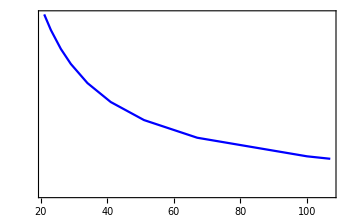
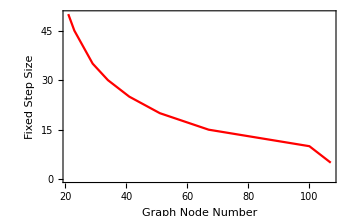
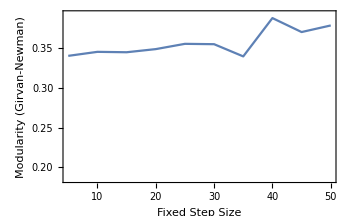
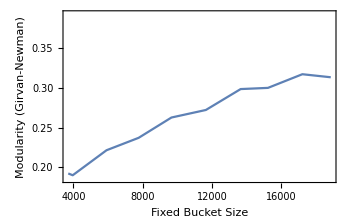

```mathematica
tickvalues={{0,0},{5000,5000},{10000,10000},{15000,15000}};
ticks=MapAt[Rotate[#,Pi/2]&,tickvalues,{All,-1}];
{Overlay[{ListLinePlot[Thread[{nodenumbers,bucketamounts}],Frame->True,ImagePadding->35,FrameTicks->{{None,ticks},{All,None}},FrameLabel->{{None,Style["Fixed Bucket Size",Blue]},{None,None}},PlotStyle->Blue,ImageSize->350,PlotRange->{{First@nodenumbers,Last@nodenumbers},All}],ListLinePlot[Thread[{nodenumbers,stepamounts}],Frame->True,ImagePadding->35,FrameTicks->{{All,None},{All,None}},FrameLabel->{"Graph Node Number",Style["Fixed Step Size",Red]},PlotStyle->Red,ImageSize->350,PlotRange->{{First@nodenumbers,Last@nodenumbers},All}]}],ListLinePlot[Thread[{stepamounts,GNmodularityvalues}],Frame->True,FrameLabel->{"Fixed Step Size","Modularity (Girvan-Newman)"},ImageSize->350,PlotRange->{{First@stepamounts,Last@stepamounts},{Min[(MinMax@GNmodularityvalues)[[1]],(MinMax@GNmodularityvaluesFixedbucket)[[1]]]-0.005,Max[(MinMax@GNmodularityvalues)[[2]],(MinMax@GNmodularityvaluesFixedbucket)[[2]]]+0.005}}](*,ListLinePlot[Thread[{Range[5,50,5],modularityvalues}],Frame->True,FrameLabel->{"Fixed Step Size","Modularity (Wolfram)"},ImageSize->350,PlotRange->Automatic]*),ListLinePlot[Thread[{bucketamounts,GNmodularityvaluesFixedbucket}],Frame->True,FrameLabel->{"Fixed Bucket Size","Modularity (Girvan-Newman)"},ImageSize->350,PlotRange->{{First@bucketamounts,Last@bucketamounts},{Min[(MinMax@GNmodularityvalues)[[1]],(MinMax@GNmodularityvaluesFixedbucket)[[1]]]-0.005,Max[(MinMax@GNmodularityvalues)[[2]],(MinMax@GNmodularityvaluesFixedbucket)[[2]]]+0.005}}](*,ListLinePlot[Thread[{graphsandnodenumbers[[All,2]],modularityvaluesFixedbucket}],Frame->True,FrameLabel->{"Fixed Bucket Size","Modularity (Wolfram)"},ImageSize->350,PlotRange->Automatic]*)}
```

```mathematica
AbsoluteTiming[thicknessdatavaryingFixedstep=Table[snetworkdatabinned[10,i,"datafull"],{i,Range@10}];]
graphsandnodenumbers=Table[snetworkgraph[thicknessdatavaryingFixedstep[[i]][[1]],thicknessdatavaryingFixedstep[[i]][[2]],1.5,7,400,RGBColor[0.1,0.5,1.]],{i,Range@10}];
GNmodularityvalues=Table[GirvanNewmanmodularity[graphsandnodenumbers[[i]][[1]]],{i,Length@graphsandnodenumbers}];
modularityvalues=Table[N@GraphAssortativity[graphsandnodenumbers[[i]][[1]],FindGraphCommunities[graphsandnodenumbers[[i]][[1]]],"Normalized"->False],{i,Length@graphsandnodenumbers}];
```

{85.8089,Null}

```mathematica
AbsoluteTiming[thicknessdatavaryingFixedbucket=Table[snetworkdatafxdbucket[10,i,"datafull"],{i,graphsandnodenumbers[[All,2]]}];]
graphsandnodenumbersFixedbucket=Table[snetworkgraph[thicknessdatavaryingFixedbucket[[i]][[1]],thicknessdatavaryingFixedbucket[[i]][[2]],1.5,7,400,RGBColor[0.1,0.5,1.]],{i,Range@10}];
GNmodularityvaluesFixedbucket=Table[GirvanNewmanmodularity[graphsandnodenumbersFixedbucket[[i]][[1]]],{i,Length@graphsandnodenumbersFixedbucket}];
modularityvaluesFixedbucket=Table[N@GraphAssortativity[graphsandnodenumbersFixedbucket[[i]][[1]],FindGraphCommunities[graphsandnodenumbersFixedbucket[[i]][[1]]],"Normalized"->False],{i,Length@graphsandnodenumbersFixedbucket}];
```

{414.264,Null}

```mathematica
stepamounts=Range@10
nodenumbers=graphsandnodenumbers[[All,2]]
bucketamounts=Table[(Values@Counts@thicknessdatavaryingFixedbucket[[i,1]])[[1]],{i,10}]
```

{1,2,3,4,5,6,7,8,9,10}

{35,19,14,11,9,8,7,6,6,5}

{11284,20832,28287,36006,44008,49512,56580,66016,66016,79216}

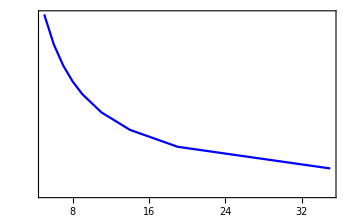
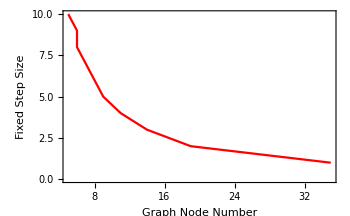
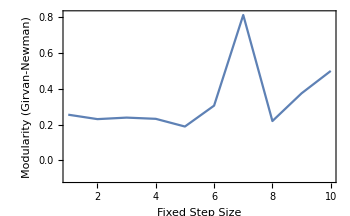
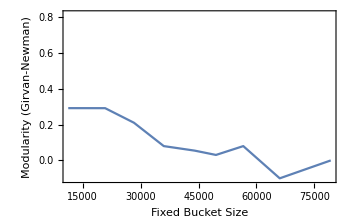

```mathematica
tickvalues={{0,0},{20000,20000},{40000,40000},{60000,60000},{80000,80000}};
ticks=MapAt[Rotate[#,Pi/2]&,tickvalues,{All,-1}];
{Overlay[{ListLinePlot[Thread[{nodenumbers,bucketamounts}],Frame->True,ImagePadding->35,FrameTicks->{{None,ticks},{All,None}},FrameLabel->{{None,Style["Fixed Bucket Size",Blue]},{None,None}},PlotStyle->Blue,ImageSize->350,PlotRange->{{First@nodenumbers,Last@nodenumbers},All}],ListLinePlot[Thread[{nodenumbers,stepamounts}],Frame->True,ImagePadding->35,FrameTicks->{{All,None},{All,None}},FrameLabel->{"Graph Node Number",Style["Fixed Step Size",Red]},PlotStyle->Red,ImageSize->350,PlotRange->{{First@nodenumbers,Last@nodenumbers},All}]}],ListLinePlot[Thread[{stepamounts,GNmodularityvalues}],Frame->True,FrameLabel->{"Fixed Step Size","Modularity (Girvan-Newman)"},ImageSize->350,PlotRange->{{First@stepamounts,Last@stepamounts},{Min[(MinMax@GNmodularityvalues)[[1]],(MinMax@GNmodularityvaluesFixedbucket)[[1]]]-0.005,Max[(MinMax@GNmodularityvalues)[[2]],(MinMax@GNmodularityvaluesFixedbucket)[[2]]]+0.005}}](*,ListLinePlot[Thread[{Range[5,50,5],modularityvalues}],Frame->True,FrameLabel->{"Fixed Step Size","Modularity (Wolfram)"},ImageSize->350,PlotRange->Automatic]*),ListLinePlot[Thread[{bucketamounts,GNmodularityvaluesFixedbucket}],Frame->True,FrameLabel->{"Fixed Bucket Size","Modularity (Girvan-Newman)"},ImageSize->350,PlotRange->{{First@bucketamounts,Last@bucketamounts},{Min[(MinMax@GNmodularityvalues)[[1]],(MinMax@GNmodularityvaluesFixedbucket)[[1]]]-0.005,Max[(MinMax@GNmodularityvalues)[[2]],(MinMax@GNmodularityvaluesFixedbucket)[[2]]]+0.005}}](*,ListLinePlot[Thread[{graphsandnodenumbers[[All,2]],modularityvaluesFixedbucket}],Frame->True,FrameLabel->{"Fixed Bucket Size","Modularity (Wolfram)"},ImageSize->350,PlotRange->Automatic]*)}
```

```mathematica
AbsoluteTiming[lengthdatavaryingFixedstep=Table[snetworkdatabinned[12,i,"datafull"],{i,Range[400,4000,400]}];]
graphsandnodenumbers=Table[snetworkgraph[lengthdatavaryingFixedstep[[i]][[1]],lengthdatavaryingFixedstep[[i]][[2]],2,7,400,RGBColor[1.,0.53,0.2]],{i,Range@10}];
GNmodularityvalues=Table[GirvanNewmanmodularity[graphsandnodenumbers[[i]][[1]]],{i,Length@graphsandnodenumbers}];
modularityvalues=Table[N@GraphAssortativity[graphsandnodenumbers[[i]][[1]],FindGraphCommunities[graphsandnodenumbers[[i]][[1]]],"Normalized"->False],{i,Length@graphsandnodenumbers}];
```

{186.044,Null}

```mathematica
AbsoluteTiming[lengthdatavaryingFixedbucket=Table[snetworkdatafxdbucket[12,i,"datafull"],{i,graphsandnodenumbers[[All,2]]}];]
graphsandnodenumbersFixedbucket=Table[snetworkgraph[lengthdatavaryingFixedbucket[[i]][[1]],lengthdatavaryingFixedbucket[[i]][[2]],2,7,400,RGBColor[1.,0.53,0.2]],{i,Range@10}];
GNmodularityvaluesFixedbucket=Table[GirvanNewmanmodularity[graphsandnodenumbersFixedbucket[[i]][[1]]],{i,Length@graphsandnodenumbersFixedbucket}];
modularityvaluesFixedbucket=Table[N@GraphAssortativity[graphsandnodenumbersFixedbucket[[i]][[1]],FindGraphCommunities[graphsandnodenumbersFixedbucket[[i]][[1]]],"Normalized"->False],{i,Length@graphsandnodenumbersFixedbucket}];
```

{90.6394,Null}

```mathematica
stepamounts=Range[400,4000,400]
nodenumbers=graphsandnodenumbers[[All,2]]
bucketamounts=Table[(Values@Counts@lengthdatavaryingFixedbucket[[i,1]])[[1]],{i,10}]
```

{400,800,1200,1600,2000,2400,2800,3200,3600,4000}

{102,54,36,28,22,20,17,16,13,12}

{3884,7336,11003,14147,18005,19805,23300,24756,30469,33008}

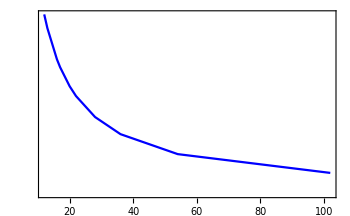
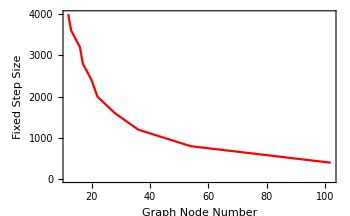
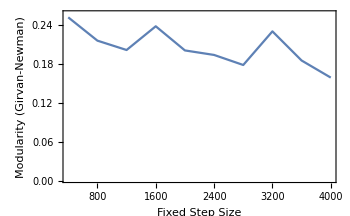
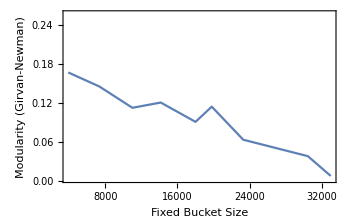

```mathematica
tickvalues={{0,0},{7000,7000},{14000,14000},{21000,21000},{28000,28000},{35000,35000}};
ticks=MapAt[Rotate[#,-Pi/2]&,tickvalues,{All,-1}];
tickvaluesst={{0,0},{1000,1000},{2000,2000},{3000,3000},{4000,4000}};
ticksst=MapAt[Rotate[#,Pi/2]&,tickvaluesst,{All,-1}];
{Overlay[{ListLinePlot[Thread[{nodenumbers,bucketamounts}],Frame->True,ImagePadding->35,FrameTicks->{{None,ticks},{All,None}},FrameLabel->{{None,Style["Fixed Bucket Size",Blue]},{None,None}},PlotStyle->Blue,ImageSize->350,PlotRange->{{First@nodenumbers,Last@nodenumbers},All}],ListLinePlot[Thread[{nodenumbers,stepamounts}],Frame->True,ImagePadding->35,FrameTicks->{{ticksst,None},{All,None}},FrameLabel->{"Graph Node Number",Style["Fixed Step Size",Red]},PlotStyle->Red,ImageSize->350,PlotRange->{{First@nodenumbers,Last@nodenumbers},All}]}],ListLinePlot[Thread[{stepamounts,GNmodularityvalues}],Frame->True,FrameLabel->{"Fixed Step Size","Modularity (Girvan-Newman)"},ImageSize->350,PlotRange->{{First@stepamounts,Last@stepamounts},{Min[(MinMax@GNmodularityvalues)[[1]],(MinMax@GNmodularityvaluesFixedbucket)[[1]]]-0.005,Max[(MinMax@GNmodularityvalues)[[2]],(MinMax@GNmodularityvaluesFixedbucket)[[2]]]+0.005}}](*,ListLinePlot[Thread[{Range[5,50,5],modularityvalues}],Frame->True,FrameLabel->{"Fixed Step Size","Modularity (Wolfram)"},ImageSize->350,PlotRange->Automatic]*),ListLinePlot[Thread[{bucketamounts,GNmodularityvaluesFixedbucket}],Frame->True,FrameLabel->{"Fixed Bucket Size","Modularity (Girvan-Newman)"},ImageSize->350,PlotRange->{{First@bucketamounts,Last@bucketamounts},{Min[(MinMax@GNmodularityvalues)[[1]],(MinMax@GNmodularityvaluesFixedbucket)[[1]]]-0.005,Max[(MinMax@GNmodularityvalues)[[2]],(MinMax@GNmodularityvaluesFixedbucket)[[2]]]+0.005}}](*,ListLinePlot[Thread[{graphsandnodenumbers[[All,2]],modularityvaluesFixedbucket}],Frame->True,FrameLabel->{"Fixed Bucket Size","Modularity (Wolfram)"},ImageSize->350,PlotRange->Automatic]*)}
```

```mathematica
test=snetworkdatabinned[11,2500,"datafull"];
graph=snetworkgraph[test[[1]],test[[2]],2,7,400,Green];
graph[[2]]
```

10

```mathematica
AbsoluteTiming[weightdatavaryingFixedstep=Table[snetworkdatabinned[11,i,"datafull"],{i,Range[200,2000,200]}];]
graphsandnodenumbers=Table[snetworkgraph[weightdatavaryingFixedstep[[i]][[1]],weightdatavaryingFixedstep[[i]][[2]],2,7,400,Red],{i,Range@10}];
GNmodularityvalues=Table[GirvanNewmanmodularity[graphsandnodenumbers[[i]][[1]]],{i,Length@graphsandnodenumbers}];
modularityvalues=Table[N@GraphAssortativity[graphsandnodenumbers[[i]][[1]],FindGraphCommunities[graphsandnodenumbers[[i]][[1]]],"Normalized"->False],{i,Length@graphsandnodenumbers}];
```

{222.935,Null}

```mathematica
AbsoluteTiming[weightdatavaryingFixedbucket=Table[snetworkdatafxdbucket[12,i,"datafull"],{i,graphsandnodenumbers[[All,2]]}];]
graphsandnodenumbersFixedbucket=Table[snetworkgraph[weightdatavaryingFixedbucket[[i]][[1]],weightdatavaryingFixedbucket[[i]][[2]],2,7,400,Red],{i,Range@10}];
GNmodularityvaluesFixedbucket=Table[GirvanNewmanmodularity[graphsandnodenumbersFixedbucket[[i]][[1]]],{i,Length@graphsandnodenumbersFixedbucket}];
modularityvaluesFixedbucket=Table[N@GraphAssortativity[graphsandnodenumbersFixedbucket[[i]][[1]],FindGraphCommunities[graphsandnodenumbersFixedbucket[[i]][[1]]],"Normalized"->False],{i,Length@graphsandnodenumbersFixedbucket}];
```

{87.715,Null}

```mathematica
stepamounts=Range[200,2000,200]
nodenumbers=graphsandnodenumbers[[All,2]]
bucketamounts=Table[(Values@Counts@weightdatavaryingFixedbucket[[i,1]])[[1]],{i,10}]
```

{200,400,600,800,1000,1200,1400,1600,1800,2000}

{110,56,38,29,23,19,18,15,14,12}

{3601,7074,10424,13659,17222,20848,22006,26407,28293,33008}

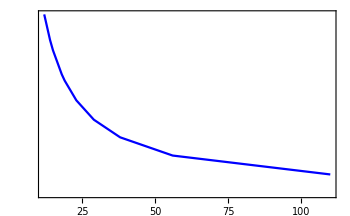
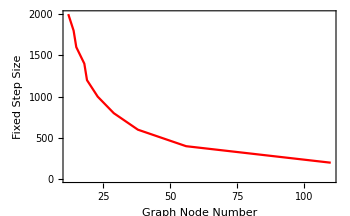
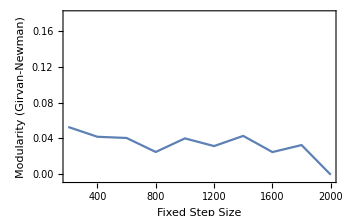
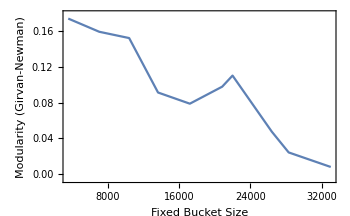

```mathematica
tickvalues={{0,0},{7000,7000},{14000,14000},{21000,21000},{28000,28000},{35000,35000}};
ticks=MapAt[Rotate[#,-Pi/2]&,tickvalues,{All,-1}];
tickvaluesst={{0,0},{500,500},{1000,1000},{1500,1500},{2000,2000}};
ticksst=MapAt[Rotate[#,Pi/2]&,tickvaluesst,{All,-1}];
{Overlay[{ListLinePlot[Thread[{nodenumbers,bucketamounts}],Frame->True,ImagePadding->35,FrameTicks->{{None,ticks},{All,None}},FrameLabel->{{None,Style["Fixed Bucket Size",Blue]},{None,None}},PlotStyle->Blue,ImageSize->350,PlotRange->{{First@nodenumbers,Last@nodenumbers},All}],ListLinePlot[Thread[{nodenumbers,stepamounts}],Frame->True,ImagePadding->35,FrameTicks->{{ticksst,None},{All,None}},FrameLabel->{"Graph Node Number",Style["Fixed Step Size",Red]},PlotStyle->Red,ImageSize->350,PlotRange->{{First@nodenumbers,Last@nodenumbers},All}]}],ListLinePlot[Thread[{stepamounts,GNmodularityvalues}],Frame->True,FrameLabel->{"Fixed Step Size","Modularity (Girvan-Newman)"},ImageSize->350,PlotRange->{{First@stepamounts,Last@stepamounts},{Min[(MinMax@GNmodularityvalues)[[1]],(MinMax@GNmodularityvaluesFixedbucket)[[1]]]-0.005,Max[(MinMax@GNmodularityvalues)[[2]],(MinMax@GNmodularityvaluesFixedbucket)[[2]]]+0.005}}](*,ListLinePlot[Thread[{Range[5,50,5],modularityvalues}],Frame->True,FrameLabel->{"Fixed Step Size","Modularity (Wolfram)"},ImageSize->350,PlotRange->Automatic]*),ListLinePlot[Thread[{bucketamounts,GNmodularityvaluesFixedbucket}],Frame->True,FrameLabel->{"Fixed Bucket Size","Modularity (Girvan-Newman)"},ImageSize->350,PlotRange->{{First@bucketamounts,Last@bucketamounts},{Min[(MinMax@GNmodularityvalues)[[1]],(MinMax@GNmodularityvaluesFixedbucket)[[1]]]-0.005,Max[(MinMax@GNmodularityvalues)[[2]],(MinMax@GNmodularityvaluesFixedbucket)[[2]]]+0.005}}](*,ListLinePlot[Thread[{graphsandnodenumbers[[All,2]],modularityvaluesFixedbucket}],Frame->True,FrameLabel->{"Fixed Bucket Size","Modularity (Wolfram)"},ImageSize->350,PlotRange->Automatic]*)}
```

Width Graphs for Varying Fixed Step Sizes and Fixed Bucket Sizes

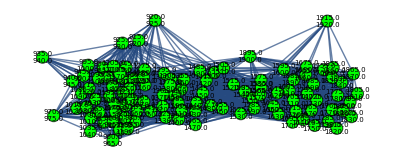
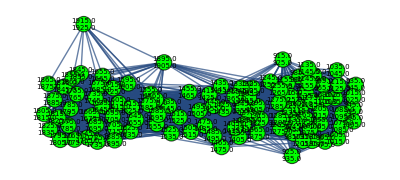
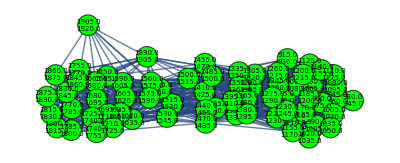
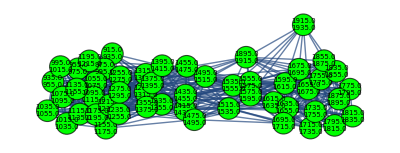
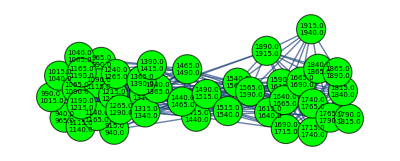
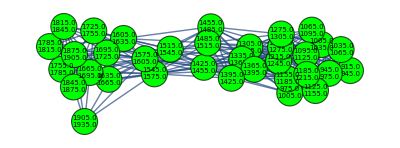
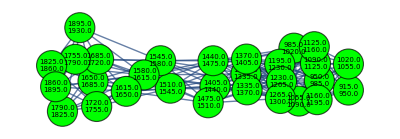
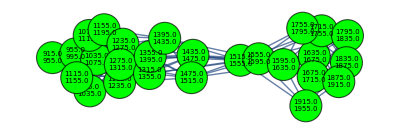
{{-Graphics-,107},{-Graphics-,100},{-Graphics-,67},{-Graphics-,51},{-Graphics-,41},{-Graphics-,34},{-Graphics-,29},{-Graphics-,26},{-Graphics-,23},{-Graphics-,21}}

```mathematica
graphsandnodenumbers
```

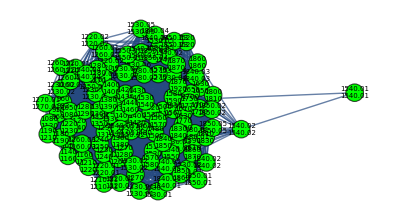
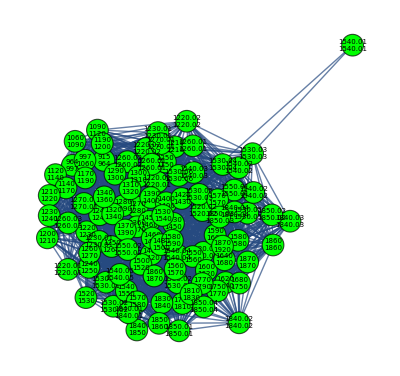
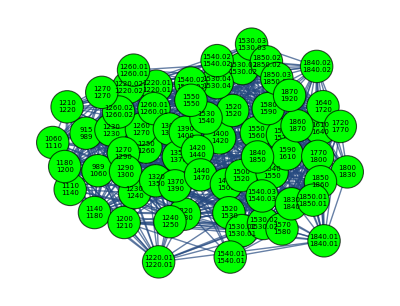
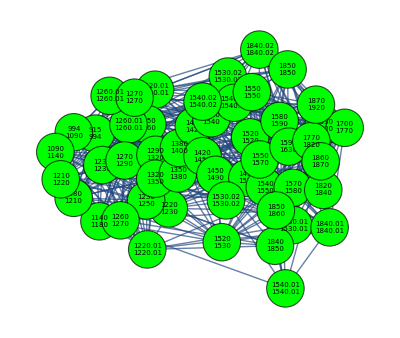
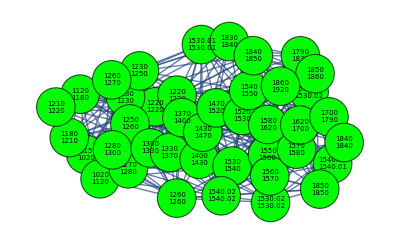
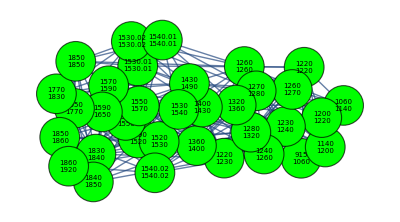
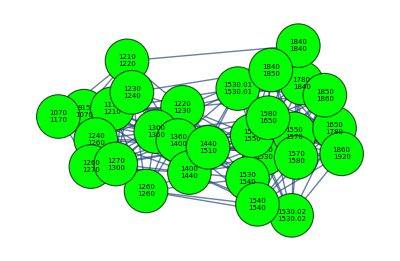
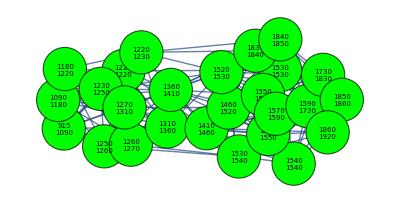
{{-Graphics-,107},{-Graphics-,100},{-Graphics-,67},{-Graphics-,51},{-Graphics-,41},{-Graphics-,34},{-Graphics-,29},{-Graphics-,26},{-Graphics-,23},{-Graphics-,21}}

```mathematica
graphsandnodenumbersFixedbucket
```

Thickness Graphs for Varying Fixed Step Sizes and Fixed Bucket Sizes

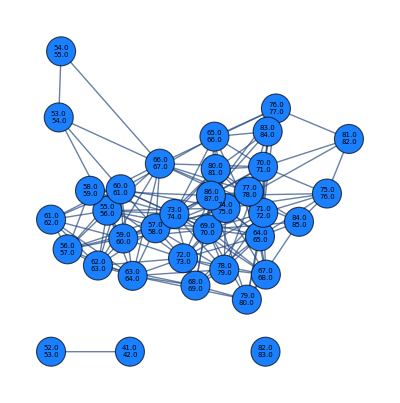
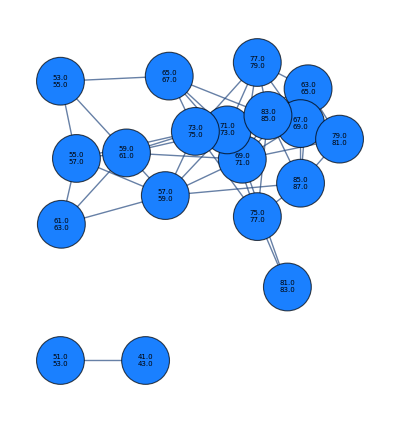
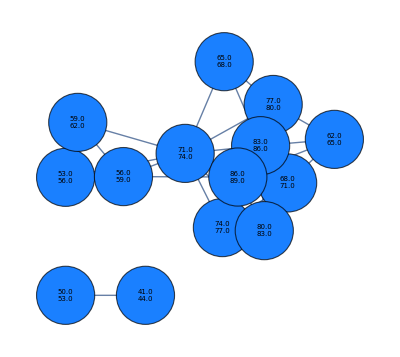
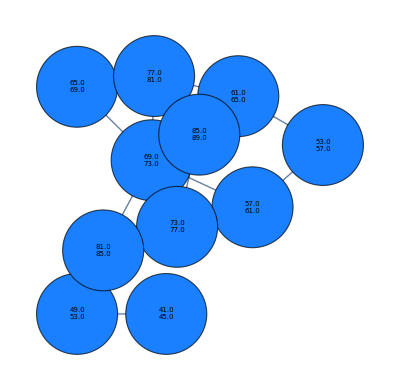
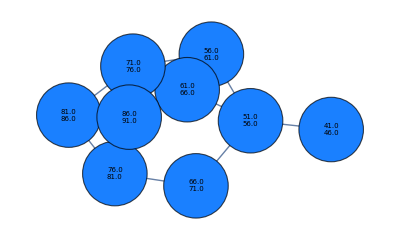
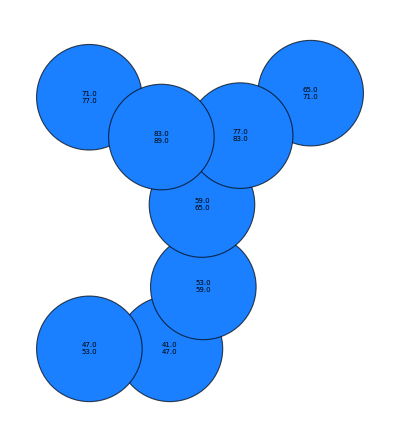
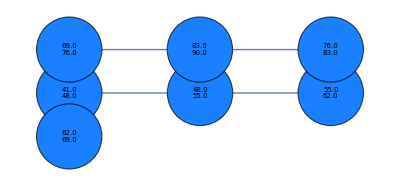
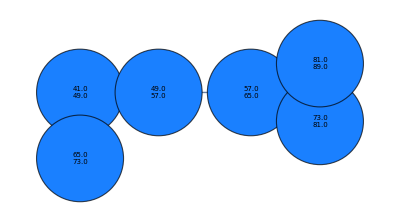
{{-Graphics-,35},{-Graphics-,19},{-Graphics-,14},{-Graphics-,11},{-Graphics-,9},{-Graphics-,8},{-Graphics-,7},{-Graphics-,6},{-Graphics-,6},{-Graphics-,5}}

```mathematica
graphsandnodenumbers
```

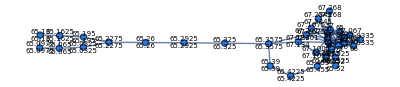
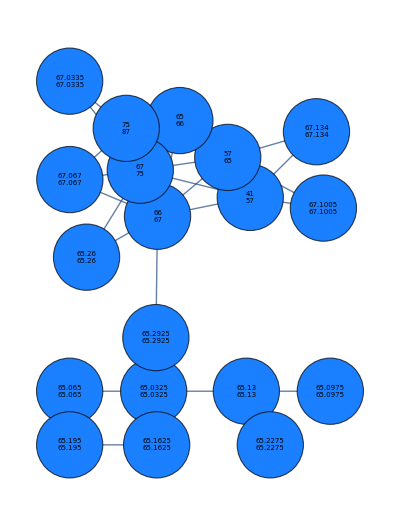
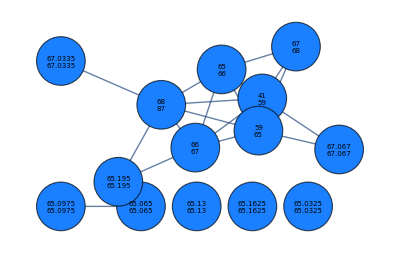
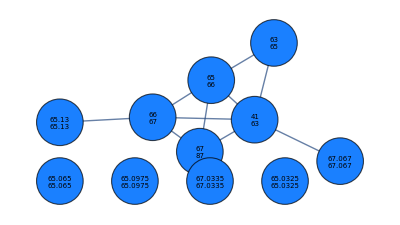
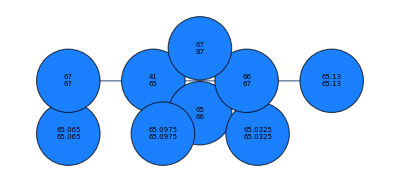
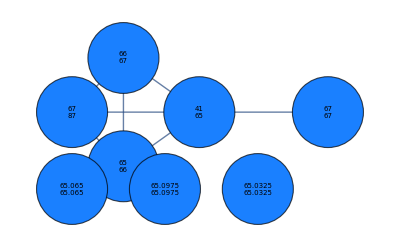
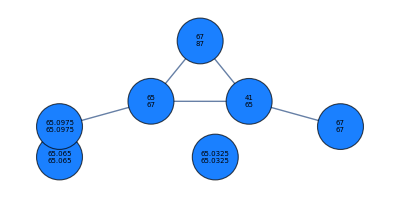
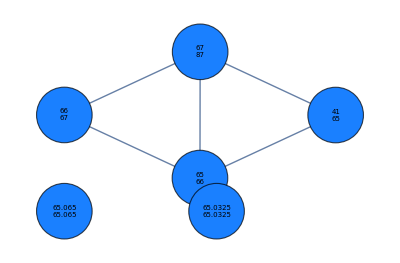
{{-Graphics-,35},{-Graphics-,19},{-Graphics-,14},{-Graphics-,11},{-Graphics-,9},{-Graphics-,8},{-Graphics-,7},{-Graphics-,6},{-Graphics-,6},{-Graphics-,5}}

```mathematica
graphsandnodenumbersFixedbucket
```

Length Graphs for Varying Fixed Step Sizes and Fixed Bucket Sizes

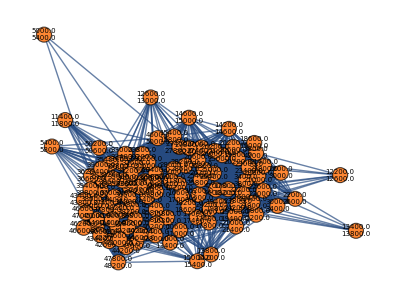
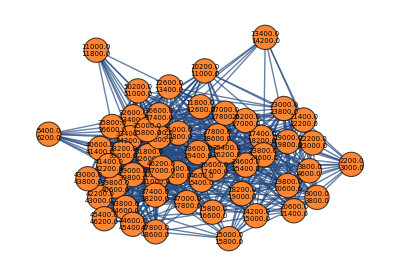
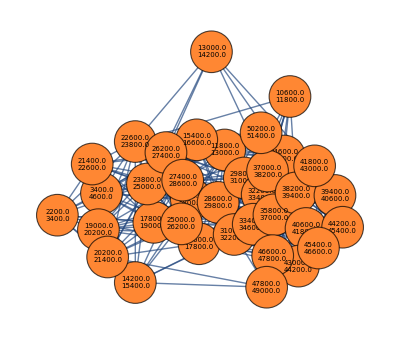
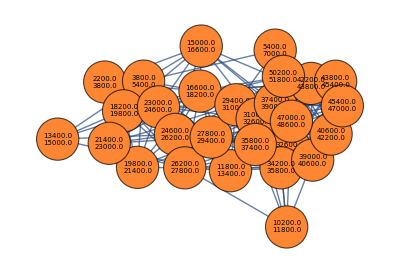
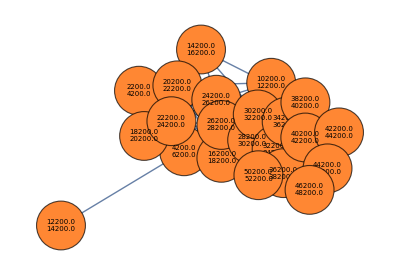
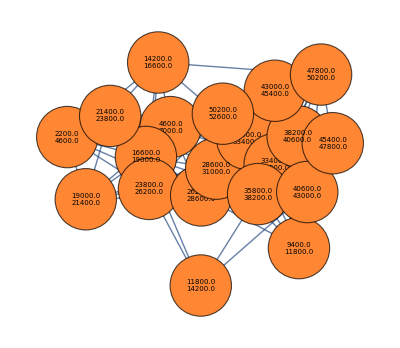
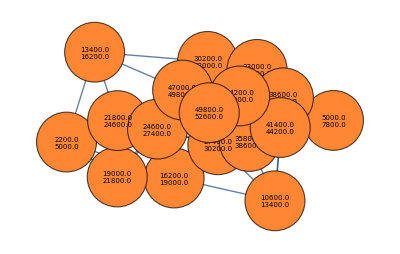
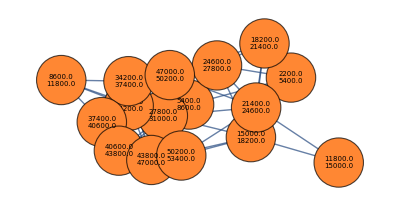
{{-Graphics-,102},{-Graphics-,54},{-Graphics-,36},{-Graphics-,28},{-Graphics-,22},{-Graphics-,20},{-Graphics-,17},{-Graphics-,16},{-Graphics-,13},{-Graphics-,12}}

```mathematica
graphsandnodenumbers
```

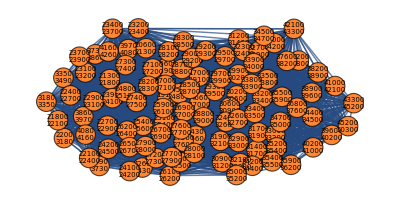
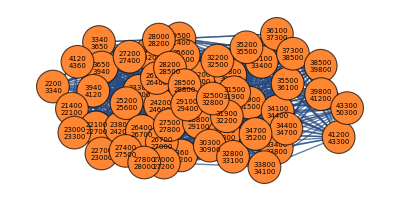
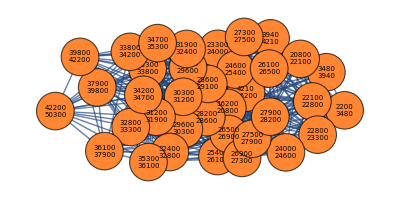
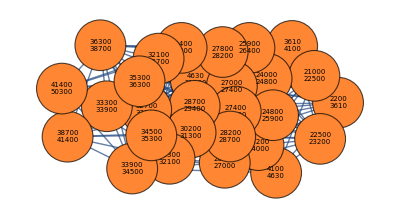
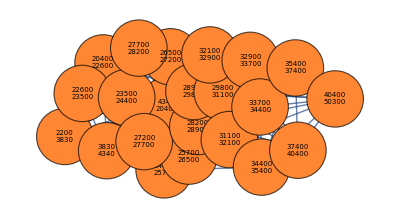
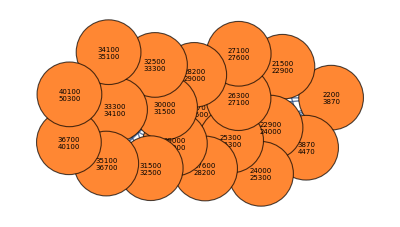
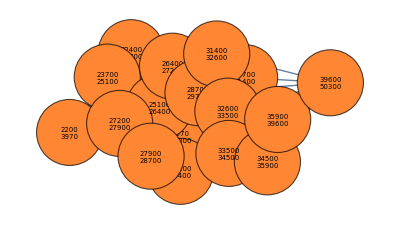
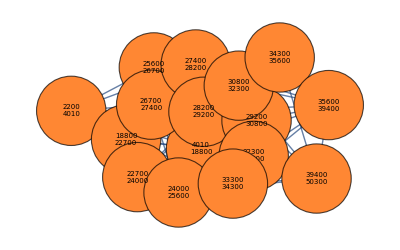
{{-Graphics-,102},{-Graphics-,54},{-Graphics-,36},{-Graphics-,28},{-Graphics-,22},{-Graphics-,20},{-Graphics-,17},{-Graphics-,16},{-Graphics-,13},{-Graphics-,12}}

```mathematica
graphsandnodenumbersFixedbucket
```

Weight Graphs for Varying Fixed Step Sizes and Fixed Bucket Sizes

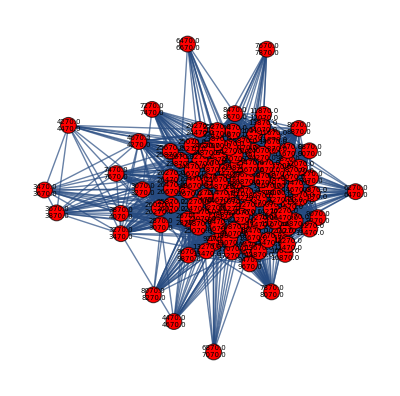
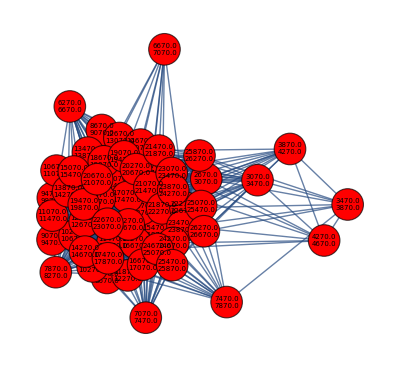
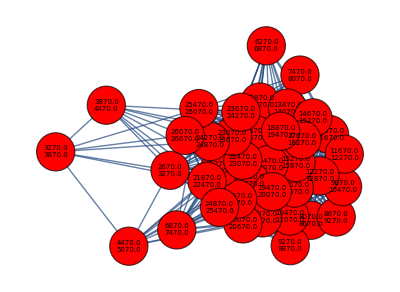
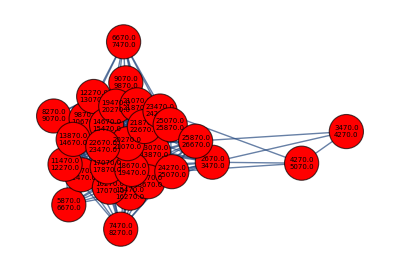
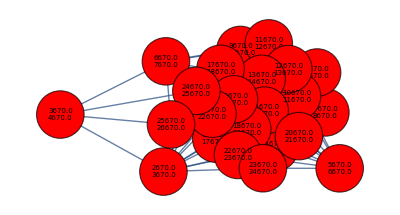
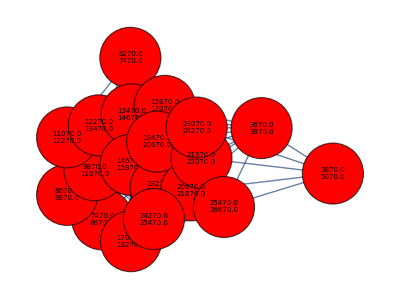
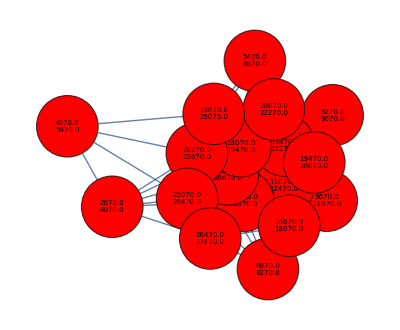
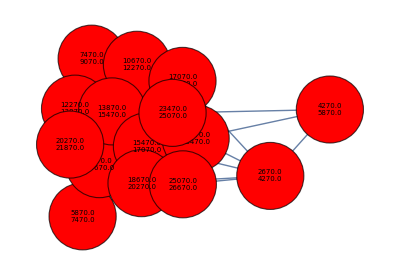
{{-Graphics-,110},{-Graphics-,56},{-Graphics-,38},{-Graphics-,29},{-Graphics-,23},{-Graphics-,19},{-Graphics-,18},{-Graphics-,15},{-Graphics-,14},{-Graphics-,12}}

```mathematica
graphsandnodenumbers
```

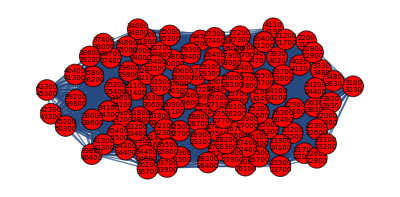
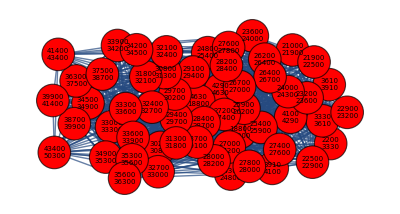
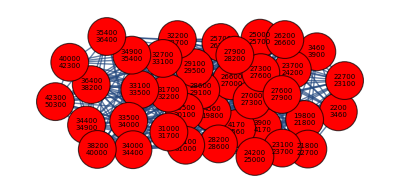
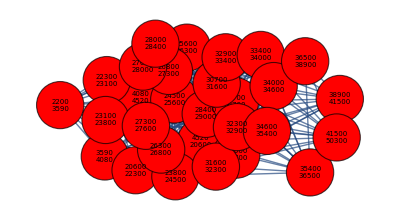
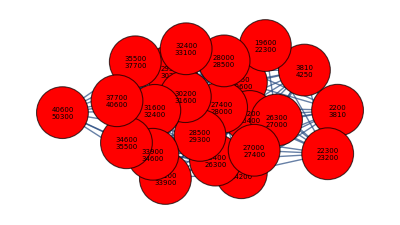
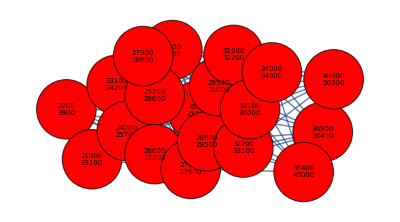
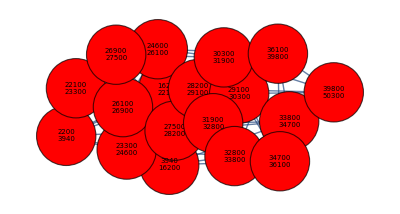
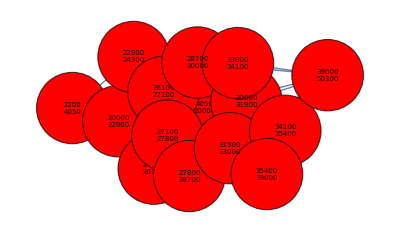
{{-Graphics-,110},{-Graphics-,56},{-Graphics-,38},{-Graphics-,29},{-Graphics-,23},{-Graphics-,19},{-Graphics-,18},{-Graphics-,15},{-Graphics-,14},{-Graphics-,12}}

```mathematica
graphsandnodenumbersFixedbucket
```

Plots Together

Fixed Step Size Networks

Width Feature

```mathematica
AbsoluteTiming[widthdataintimewindowsFixedstep=snetworkdatabinnedintimewindows[9,15,10];]
```

{342.845,Null}

```mathematica
graphsandnodenumbers=Table[snetworkgraph[widthdataintimewindowsFixedstep[[1]][[i]],widthdataintimewindowsFixedstep[[2]][[i]],2,7,400,Green],{i,Range@10}];
```

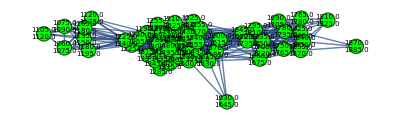
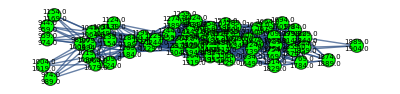
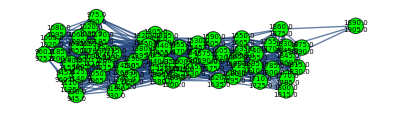
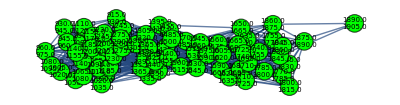
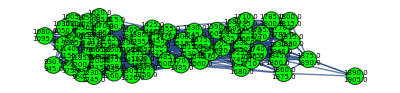
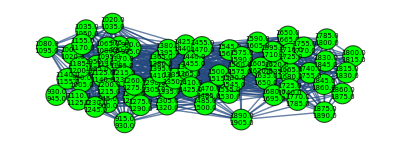
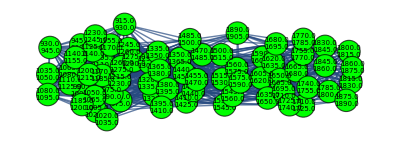
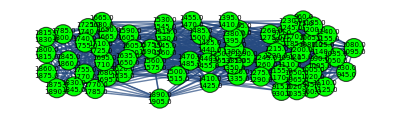
{{-Graphics-,52},{-Graphics-,63},{-Graphics-,66},{-Graphics-,66},{-Graphics-,66},{-Graphics-,66},{-Graphics-,66},{-Graphics-,66},{-Graphics-,66},{-Graphics-,67}}

```mathematica
graphsandnodenumbers
```

```mathematica
ABCvalues=Table[Mean@BetweennessCentrality[graphsandnodenumbers[[i]][[1]]],{i,Length@graphsandnodenumbers}];
modularityvalues=Table[N@GraphAssortativity[graphsandnodenumbers[[i]][[1]],FindGraphCommunities[graphsandnodenumbers[[i]][[1]]],"Normalized"->False],{i,Length@graphsandnodenumbers}];
degreevalues=Table[N@Mean@VertexDegree[graphsandnodenumbers[[i]][[1]]],{i,Length@graphsandnodenumbers}];
```

```mathematica
singlerandomgraphs=Table[RandomGraph[{VertexCount[i],EdgeCount[i]}],{i,graphsandnodenumbers[[All,1]]}];
singlerandomGNmodularityvalues=Table[GirvanNewmanmodularity[singlerandomgraphs[[i]]],{i,Length@singlerandomgraphs}];
```

```mathematica
GNmodularityvalues=Table[GirvanNewmanmodularity[graphsandnodenumbers[[i]][[1]]],{i,Length@graphsandnodenumbers}];
```

```mathematica
Zscoremodularity=Table[randomnessfunctionformodularity[i,1],{i,graphsandnodenumbers[[All,1]]}];
```

```mathematica
Table[Length@FindGraphCommunities[graphsandnodenumbers[[i]][[1]]],{i,Length@graphsandnodenumbers}]
```

{3,3,3,2,2,2,2,2,2,3}

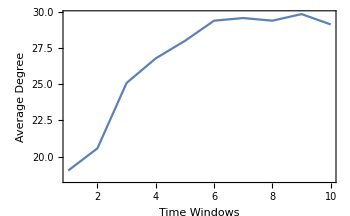
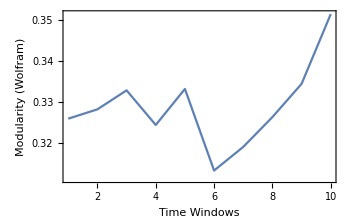
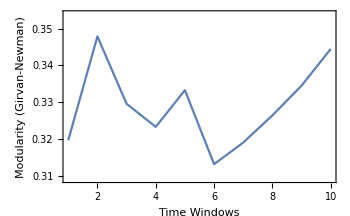
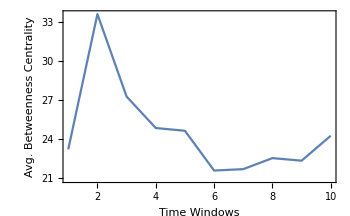
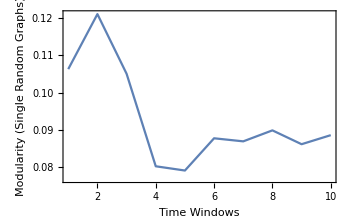
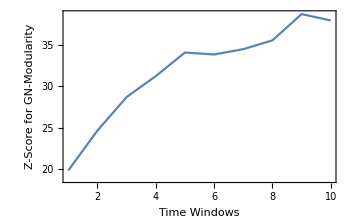

```mathematica
{ListLinePlot[Thread[{Range@10,degreevalues}],Frame->True,FrameLabel->{"Time Windows","Average Degree"},ImageSize->350,PlotRange->{{1,10},All}],ListLinePlot[Thread[{Range@10,modularityvalues}],Frame->True,FrameLabel->{"Time Windows","Modularity (Wolfram)"},ImageSize->350,PlotRange->{{1,10},All}],ListLinePlot[Thread[{Range@10,GNmodularityvalues}],Frame->True,FrameLabel->{"Time Windows","Modularity (Girvan-Newman)"},ImageSize->350,PlotRange->{{1,10},{0.309,0.354}}],ListLinePlot[Thread[{Range@10,ABCvalues}],Frame->True,FrameLabel->{"Time Windows","Avg. Betweenness Centrality"},ImageSize->350,PlotRange->{{1,10},All}],ListLinePlot[Thread[{Range@10,singlerandomGNmodularityvalues}],Frame->True,FrameLabel->{"Time Windows","Modularity (Single Random Graphs)"},ImageSize->350,PlotRange->{{1,10},All}],ListLinePlot[Thread[{Range@10,Zscoremodularity[[All,1]]}],Frame->True,FrameLabel->{"Time Windows","Z-Score for GN-Modularity"},ImageSize->350,PlotRange->{{1,10},{17.5,40}}]}
```

```mathematica
Zscoremodularityswitch=Table[randomnessfunctionformodularity[i,2],{i,graphsandnodenumbers[[All,1]]}];
```

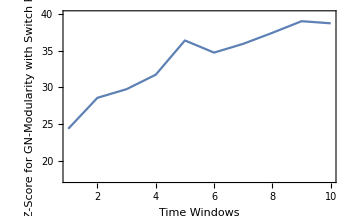

```mathematica
ListLinePlot[Thread[{Range@10,Zscoremodularityswitch[[All,1]]}],Frame->True,FrameLabel->{"Time Windows","Z-Score for GN-Modularity with Switch Rnd."},ImageSize->350,PlotRange->{{1,10},{17.5,40}}]
```

Thickness Feature

```mathematica
AbsoluteTiming[thicknessdataintimewindowsFixedstep=snetworkdatabinnedintimewindows[10,0.2,10];]
```

{617.113,Null}

```mathematica
graphsandnodenumbers=Table[snetworkgraph[thicknessdataintimewindowsFixedstep[[1]][[i]],thicknessdataintimewindowsFixedstep[[2]][[i]],2,7,400,RGBColor[0.1,0.5,1.]],{i,Range@10}];
```

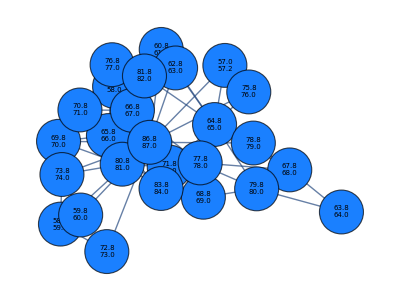
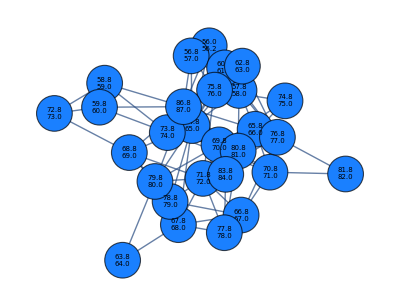
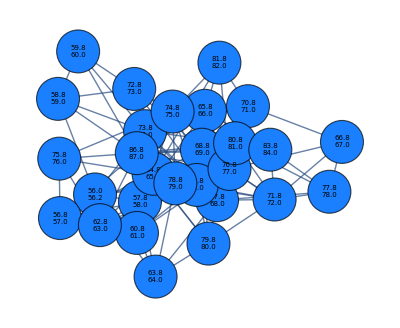
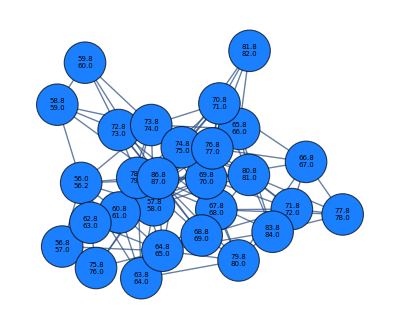
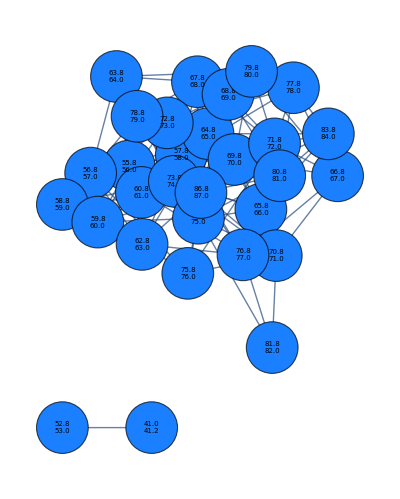
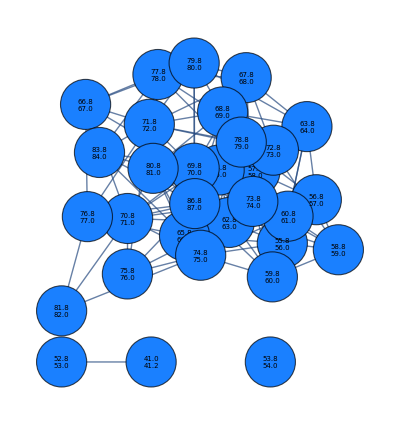
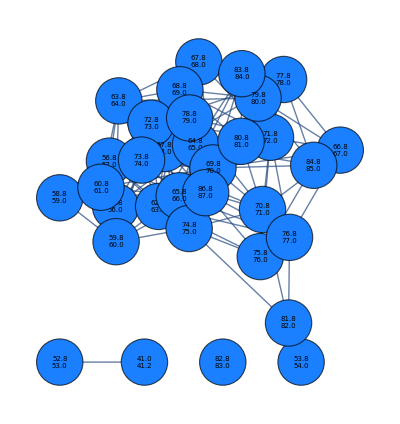
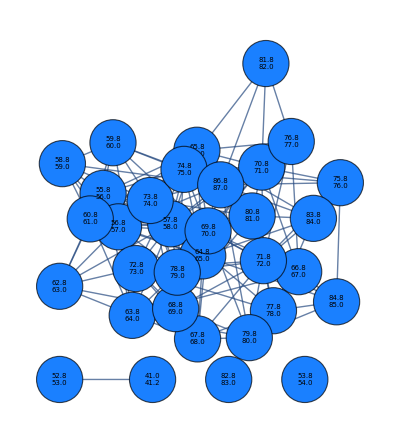
{{-Graphics-,26},{-Graphics-,28},{-Graphics-,28},{-Graphics-,28},{-Graphics-,30},{-Graphics-,31},{-Graphics-,33},{-Graphics-,33},{-Graphics-,35},{-Graphics-,35}}

```mathematica
graphsandnodenumbers
```

```mathematica
ABCvalues=Table[Mean@BetweennessCentrality[graphsandnodenumbers[[i]][[1]]],{i,Length@graphsandnodenumbers}];
modularityvalues=Table[N@GraphAssortativity[graphsandnodenumbers[[i]][[1]],FindGraphCommunities[graphsandnodenumbers[[i]][[1]]],"Normalized"->False],{i,Length@graphsandnodenumbers}];
degreevalues=Table[N@Mean@VertexDegree[graphsandnodenumbers[[i]][[1]]],{i,Length@graphsandnodenumbers}];
```

```mathematica
singlerandomgraphs=Table[RandomGraph[{VertexCount[i],EdgeCount[i]}],{i,graphsandnodenumbers[[All,1]]}];
singlerandomGNmodularityvalues=Table[GirvanNewmanmodularity[singlerandomgraphs[[i]]],{i,Length@singlerandomgraphs}];
```

```mathematica
GNmodularityvalues=Table[GirvanNewmanmodularity[graphsandnodenumbers[[i]][[1]]],{i,Length@graphsandnodenumbers}];
```

```mathematica
Zscoremodularity=Table[randomnessfunctionformodularity[i,1],{i,graphsandnodenumbers[[All,1]]}];
```

```mathematica
Table[Length@FindGraphCommunities[graphsandnodenumbers[[i]][[1]]],{i,Length@graphsandnodenumbers}]
```

{4,4,4,4,4,4,6,5,5,4}

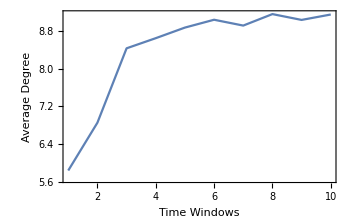
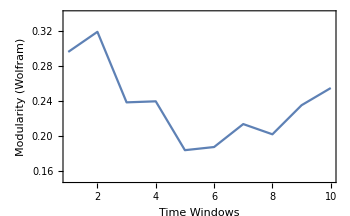
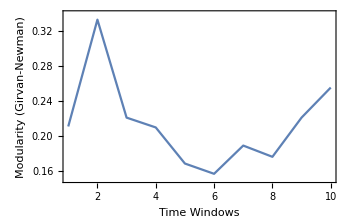
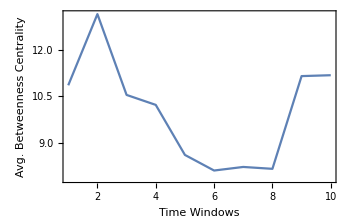
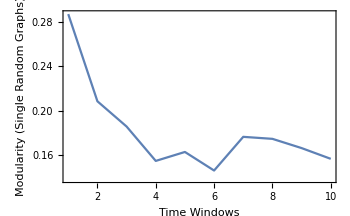
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
{ListLinePlot[Thread[{Range@10,degreevalues}],Frame->True,FrameLabel->{"Time Windows","Average Degree"},ImageSize->350,PlotRange->{{1,10},All}],ListLinePlot[Thread[{Range@10,modularityvalues}],Frame->True,FrameLabel->{"Time Windows","Modularity (Wolfram)"},ImageSize->350,PlotRange->{{1,10},{0.15,0.34}}],ListLinePlot[Thread[{Range@10,GNmodularityvalues}],Frame->True,FrameLabel->{"Time Windows","Modularity (Girvan-Newman)"},ImageSize->350,PlotRange->{{1,10},{0.15,0.34}}],ListLinePlot[Thread[{Range@10,ABCvalues}],Frame->True,FrameLabel->{"Time Windows","Avg. Betweenness Centrality"},ImageSize->350,PlotRange->{{1,10},All}],ListLinePlot[Thread[{Range@10,singlerandomGNmodularityvalues}],Frame->True,FrameLabel->{"Time Windows","Modularity (Single Random Graphs)"},ImageSize->350,PlotRange->{{1,10},All}],ListLinePlot[Thread[{Range@10,Zscoremodularity[[All,1]]}],Frame->True,FrameLabel->{"Time Windows","Z-Score for GN-Modularity"},ImageSize->350,PlotRange->{{1,10},{-0.9,6.5}}]}
```

```mathematica
Zscoremodularityswitch=Table[randomnessfunctionformodularity[i,2],{i,graphsandnodenumbers[[All,1]]}];
```

```mathematica
ListLinePlot[Thread[{Range@10,Zscoremodularityswitch[[All,1]]}],Frame->True,FrameLabel->{"Time Windows","Z-Score for GN-Modularity with Switch Rnd."},ImageSize->350,PlotRange->{{1,10},{-0.9,6.5}}]
```

-Graphics-

Length Feature

```mathematica
AbsoluteTiming[lengthdataintimewindowsFixedstep=snetworkdatabinnedintimewindows[12,600,10];]
```

{229.445,Null}

```mathematica
graphsandnodenumbers=Table[snetworkgraph[lengthdataintimewindowsFixedstep[[1]][[i]],lengthdataintimewindowsFixedstep[[2]][[i]],2,7,400,RGBColor[1.,0.53,0.2]],{i,Range@10}];
```

```mathematica
graphsandnodenumbers
```

{{-Graphics-,61},{-Graphics-,67},{-Graphics-,67},{-Graphics-,68},{-Graphics-,69},{-Graphics-,69},{-Graphics-,69},{-Graphics-,69},{-Graphics-,70},{-Graphics-,70}}

```mathematica
ABCvalues=Table[Mean@BetweennessCentrality[graphsandnodenumbers[[i]][[1]]],{i,Length@graphsandnodenumbers}];
modularityvalues=Table[N@GraphAssortativity[graphsandnodenumbers[[i]][[1]],FindGraphCommunities[graphsandnodenumbers[[i]][[1]]],"Normalized"->False],{i,Length@graphsandnodenumbers}];
degreevalues=Table[N@Mean@VertexDegree[graphsandnodenumbers[[i]][[1]]],{i,Length@graphsandnodenumbers}];
```

```mathematica
GNmodularityvalues=Table[GirwanNewmanmodularity[graphsandnodenumbers[[i]][[1]]],{i,Length@graphsandnodenumbers}];
```

```mathematica
Table[Length@FindGraphCommunities[graphsandnodenumbers[[i]][[1]]],{i,Length@graphsandnodenumbers}]
```

{2,2,2,2,2,2,2,2,2,2}

```mathematica
{ListLinePlot[Thread[{Range@10,degreevalues}],Frame->True,FrameLabel->{"Time Windows","Average Degree"},ImageSize->350,PlotRange->{{1,10},All}],ListLinePlot[Thread[{Range@10,ABCvalues}],Frame->True,FrameLabel->{"Time Windows","Avg. Betweenness Centrality"},ImageSize->350,PlotRange->{{1,10},All}],ListLinePlot[Thread[{Range@10,modularityvalues}],Frame->True,FrameLabel->{"Time Windows","Modularity (Wolfram)"},ImageSize->350,PlotRange->{{1,10},All}],ListLinePlot[Thread[{Range@10,GNmodularityvalues}],Frame->True,FrameLabel->{"Time Windows","Modularity (Girwan-Newman)"},ImageSize->350,PlotRange->{{1,10},All}]}
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Weight Feature

```mathematica
AbsoluteTiming[weightdataintimewindowsFixedstep=snetworkdatabinnedintimewindows[11,600,10];]
```

{164.225,Null}

```mathematica
graphsandnodenumbers=Table[snetworkgraph[weightdataintimewindowsFixedstep[[1]][[i]],weightdataintimewindowsFixedstep[[2]][[i]],2,7,400,Red],{i,Range@10}];
```

```mathematica
graphsandnodenumbers
```

{{-Graphics-,35},{-Graphics-,36},{-Graphics-,37},{-Graphics-,38},{-Graphics-,38},{-Graphics-,38},{-Graphics-,38},{-Graphics-,38},{-Graphics-,38},{-Graphics-,38}}

```mathematica
ABCvalues=Table[Mean@BetweennessCentrality[graphsandnodenumbers[[i]][[1]]],{i,Length@graphsandnodenumbers}];
modularityvalues=Table[N@GraphAssortativity[graphsandnodenumbers[[i]][[1]],FindGraphCommunities[graphsandnodenumbers[[i]][[1]]],"Normalized"->False],{i,Length@graphsandnodenumbers}];
degreevalues=Table[N@Mean@VertexDegree[graphsandnodenumbers[[i]][[1]]],{i,Length@graphsandnodenumbers}];
```

```mathematica
GNmodularityvalues=Table[GirwanNewmanmodularity[graphsandnodenumbers[[i]][[1]]],{i,Length@graphsandnodenumbers}];
```

```mathematica
Table[Length@FindGraphCommunities[graphsandnodenumbers[[i]][[1]]],{i,Length@graphsandnodenumbers}]
```

{3,3,3,3,2,2,2,2,2,2}

```mathematica
{ListLinePlot[Thread[{Range@10,degreevalues}],Frame->True,FrameLabel->{"Time Windows","Average Degree"},ImageSize->350,PlotRange->{{1,10},All}],ListLinePlot[Thread[{Range@10,ABCvalues}],Frame->True,FrameLabel->{"Time Windows","Avg. Betweenness Centrality"},ImageSize->350,PlotRange->{{1,10},All}],ListLinePlot[Thread[{Range@10,modularityvalues}],Frame->True,FrameLabel->{"Time Windows","Modularity (Wolfram)"},ImageSize->350,PlotRange->{{1,10},All}],ListLinePlot[Thread[{Range@10,GNmodularityvalues}],Frame->True,FrameLabel->{"Time Windows","Modularity (Girwan-Newman)"},ImageSize->350,PlotRange->{{1,10},All}]}
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Fixed Bucket Size Networks

Width Feature

```mathematica
AbsoluteTiming[widthdataintimewindowsFixedbucket=snetworkdatafxdbucketintimewindows[9,60,10];]
```

{992.259,Null}

```mathematica
graphsandnodenumbers=Table[snetworkgraph[widthdataintimewindowsFixedbucket[[1]][[i]],widthdataintimewindowsFixedbucket[[2]][[i]],1.5,7,400,Green],{i,Range@10}];
```

```mathematica
graphsandnodenumbers
```

{{-Graphics-,60},{-Graphics-,60},{-Graphics-,60},{-Graphics-,60},{-Graphics-,60},{-Graphics-,60},{-Graphics-,60},{-Graphics-,60},{-Graphics-,60},{-Graphics-,60}}

```mathematica
ABCvalues=Table[Mean@BetweennessCentrality[graphsandnodenumbers[[i]][[1]]],{i,Length@graphsandnodenumbers}];
modularityvalues=Table[N@GraphAssortativity[graphsandnodenumbers[[i]][[1]],FindGraphCommunities[graphsandnodenumbers[[i]][[1]]],"Normalized"->False],{i,Length@graphsandnodenumbers}];
degreevalues=Table[N@Mean@VertexDegree[graphsandnodenumbers[[i]][[1]]],{i,Length@graphsandnodenumbers}];
```

```mathematica
singlerandomgraphs=Table[RandomGraph[{VertexCount[i],EdgeCount[i]}],{i,graphsandnodenumbers[[All,1]]}];
singlerandomGNmodularityvalues=Table[GirvanNewmanmodularity[singlerandomgraphs[[i]]],{i,Length@singlerandomgraphs}];
```

```mathematica
GNmodularityvalues=Table[GirvanNewmanmodularity[graphsandnodenumbers[[i]][[1]]],{i,Length@graphsandnodenumbers}];
```

```mathematica
Zscoremodularity=Table[randomnessfunctionformodularity[i,1],{i,graphsandnodenumbers[[All,1]]}];
```

```mathematica
Table[Length@FindGraphCommunities[graphsandnodenumbers[[i]][[1]]],{i,Length@graphsandnodenumbers}]
```

{2,3,2,3,3,2,2,3,2,2}

```mathematica
{ListLinePlot[Thread[{Range@10,degreevalues}],Frame->True,FrameLabel->{"Time Windows","Average Degree"},ImageSize->350,PlotRange->{{1,10},All}],ListLinePlot[Thread[{Range@10,modularityvalues}],Frame->True,FrameLabel->{"Time Windows","Modularity (Wolfram)"},ImageSize->350,PlotRange->{{1,10},{0.12,0.265}}],ListLinePlot[Thread[{Range@10,GNmodularityvalues}],Frame->True,FrameLabel->{"Time Windows","Modularity (Girvan-Newman)"},ImageSize->350,PlotRange->{{1,10},{0.12,0.265}}],ListLinePlot[Thread[{Range@10,singlerandomGNmodularityvalues}],Frame->True,FrameLabel->{"Time Windows","Modularity (Single Random Graphs)"},ImageSize->350,PlotRange->{{1,10},All}],ListLinePlot[Thread[{Range@10,ABCvalues}],Frame->True,FrameLabel->{"Time Windows","Avg. Betweenness Centrality"},ImageSize->350,PlotRange->{{1,10},All}],ListLinePlot[Thread[{Range@10,Zscoremodularity[[All,1]]}],Frame->True,FrameLabel->{"Time Windows","Z-Score for GN-Modularity"},ImageSize->350,PlotRange->{{1,10},All}]}
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Zscoremodularityswitch=Table[randomnessfunctionformodularity[i,2],{i,graphsandnodenumbers[[All,1]]}];
```

```mathematica
ListLinePlot[Thread[{Range@10,Zscoremodularityswitch[[All,1]]}],Frame->True,FrameLabel->{"Time Windows","Z-Score for GN-Modularity with Switch Rnd."},ImageSize->350,PlotRange->{{1,10},{0,27}}]
```

-Graphics-

Thickness Feature

```mathematica
AbsoluteTiming[thicknessdataintimewindowsFixedbucket=snetworkdatafxdbucketintimewindows[10,32,10];]
```

{3094.31,Null}

```mathematica
graphsandnodenumbers=Table[snetworkgraph[thicknessdataintimewindowsFixedbucket[[1]][[i]],thicknessdataintimewindowsFixedbucket[[2]][[i]],1.5,7,400,RGBColor[0.1,0.5,1.]],{i,Range@10}];
```

```mathematica
graphsandnodenumbers
```

{{-Graphics-,32},{-Graphics-,32},{-Graphics-,32},{-Graphics-,32},{-Graphics-,32},{-Graphics-,32},{-Graphics-,32},{-Graphics-,32},{-Graphics-,32},{-Graphics-,32}}

```mathematica
ABCvalues=Table[Mean@BetweennessCentrality[graphsandnodenumbers[[i]][[1]]],{i,Length@graphsandnodenumbers}];
modularityvalues=Table[N@GraphAssortativity[graphsandnodenumbers[[i]][[1]],FindGraphCommunities[graphsandnodenumbers[[i]][[1]]],"Normalized"->False],{i,Length@graphsandnodenumbers}];
degreevalues=Table[N@Mean@VertexDegree[graphsandnodenumbers[[i]][[1]]],{i,Length@graphsandnodenumbers}];
```

```mathematica
singlerandomgraphs=Table[RandomGraph[{VertexCount[i],EdgeCount[i]}],{i,graphsandnodenumbers[[All,1]]}];
singlerandomGNmodularityvalues=Table[GirvanNewmanmodularity[singlerandomgraphs[[i]]],{i,Length@singlerandomgraphs}];
```

```mathematica
GNmodularityvalues=Table[GirvanNewmanmodularity[graphsandnodenumbers[[i]][[1]]],{i,Length@graphsandnodenumbers}];
```

```mathematica
Zscoremodularity=Table[randomnessfunctionformodularity[i,1],{i,graphsandnodenumbers[[All,1]]}];
```

```mathematica
Table[Length@FindGraphCommunities[graphsandnodenumbers[[i]][[1]]],{i,Length@graphsandnodenumbers}]
```

{3,4,3,4,4,4,4,4,4,4}

```mathematica
{ListLinePlot[Thread[{Range@10,degreevalues}],Frame->True,FrameLabel->{"Time Windows","Average Degree"},ImageSize->350,PlotRange->{{1,10},All}],ListLinePlot[Thread[{Range@10,modularityvalues}],Frame->True,FrameLabel->{"Time Windows","Modularity (Wolfram)"},ImageSize->350,PlotRange->{{1,10},{0.25,0.45}}],ListLinePlot[Thread[{Range@10,GNmodularityvalues}],Frame->True,FrameLabel->{"Time Windows","Modularity (Girvan-Newman)"},ImageSize->350,PlotRange->{{1,10},{0.25,0.45}}],ListLinePlot[Thread[{Range@10,ABCvalues}],Frame->True,FrameLabel->{"Time Windows","Avg. Betweenness Centrality"},ImageSize->350,PlotRange->{{1,10},All}],ListLinePlot[Thread[{Range@10,singlerandomGNmodularityvalues}],Frame->True,FrameLabel->{"Time Windows","Modularity (Single Random Graphs)"},ImageSize->350,PlotRange->{{1,10},All}],ListLinePlot[Thread[{Range@10,Zscoremodularity[[All,1]]}],Frame->True,FrameLabel->{"Time Windows","Z-Score for GN-Modularity"},ImageSize->350,PlotRange->{{1,10},{0,6}}]}
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Zscoremodularityswitch=Table[randomnessfunctionformodularity[i,2],{i,graphsandnodenumbers[[All,1]]}];
```

```mathematica
ListLinePlot[Thread[{Range@10,Zscoremodularityswitch[[All,1]]}],Frame->True,FrameLabel->{"Time Windows","Z-Score for GN-Modularity with Switch Rnd."},ImageSize->350,PlotRange->{{1,10},{0,8}}]
```

-Graphics-

Length Feature

```mathematica
AbsoluteTiming[lengthdataintimewindowsFixedbucket=snetworkdatafxdbucketintimewindows[12,65,10];]
```

{917.129,Null}

```mathematica
graphsandnodenumbers=Table[snetworkgraph[lengthdataintimewindowsFixedbucket[[1]][[i]],lengthdataintimewindowsFixedbucket[[2]][[i]],1.5,7,400,RGBColor[1.,0.53,0.2]],{i,Range@10}];
```

```mathematica
graphsandnodenumbers
```

{{-Graphics-,65},{-Graphics-,65},{-Graphics-,65},{-Graphics-,65},{-Graphics-,65},{-Graphics-,65},{-Graphics-,65},{-Graphics-,65},{-Graphics-,65},{-Graphics-,65}}

```mathematica
ABCvalues=Table[Mean@BetweennessCentrality[graphsandnodenumbers[[i]][[1]]],{i,Length@graphsandnodenumbers}];
modularityvalues=Table[N@GraphAssortativity[graphsandnodenumbers[[i]][[1]],FindGraphCommunities[graphsandnodenumbers[[i]][[1]]],"Normalized"->False],{i,Length@graphsandnodenumbers}];
degreevalues=Table[N@Mean@VertexDegree[graphsandnodenumbers[[i]][[1]]],{i,Length@graphsandnodenumbers}];
```

```mathematica
GNmodularityvalues=Table[GirwanNewmanmodularity[graphsandnodenumbers[[i]][[1]]],{i,Length@graphsandnodenumbers}];
```

```mathematica
Table[Length@FindGraphCommunities[graphsandnodenumbers[[i]][[1]]],{i,Length@graphsandnodenumbers}]
```

{2,2,2,2,2,2,2,2,2,2}

```mathematica
{ListLinePlot[Thread[{Range@10,degreevalues}],Frame->True,FrameLabel->{"Time Windows","Average Degree"},ImageSize->350,PlotRange->{{1,10},All}],ListLinePlot[Thread[{Range@10,ABCvalues}],Frame->True,FrameLabel->{"Time Windows","Avg. Betweenness Centrality"},ImageSize->350,PlotRange->{{1,10},All}],ListLinePlot[Thread[{Range@10,modularityvalues}],Frame->True,FrameLabel->{"Time Windows","Modularity (Wolfram)"},ImageSize->350,PlotRange->{{1,10},All}],ListLinePlot[Thread[{Range@10,GNmodularityvalues}],Frame->True,FrameLabel->{"Time Windows","Modularity (Girwan-Newman)"},ImageSize->350,PlotRange->{{1,10},All}]}
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Weight Feature

```mathematica
AbsoluteTiming[weightdataintimewindowsFixedbucket=snetworkdatafxdbucketintimewindows[11,38,10];]
```

{2015.52,Null}

```mathematica
graphsandnodenumbers=Table[snetworkgraph[weightdataintimewindowsFixedbucket[[1]][[i]],weightdataintimewindowsFixedbucket[[2]][[i]],1.5,7,400,Red],{i,Range@10}];
```

```mathematica
graphsandnodenumbers
```

{{-Graphics-,38},{-Graphics-,38},{-Graphics-,38},{-Graphics-,38},{-Graphics-,38},{-Graphics-,38},{-Graphics-,38},{-Graphics-,38},{-Graphics-,38},{-Graphics-,38}}

```mathematica
ABCvalues=Table[Mean@BetweennessCentrality[graphsandnodenumbers[[i]][[1]]],{i,Length@graphsandnodenumbers}];
modularityvalues=Table[N@GraphAssortativity[graphsandnodenumbers[[i]][[1]],FindGraphCommunities[graphsandnodenumbers[[i]][[1]]],"Normalized"->False],{i,Length@graphsandnodenumbers}];
degreevalues=Table[N@Mean@VertexDegree[graphsandnodenumbers[[i]][[1]]],{i,Length@graphsandnodenumbers}];
```

```mathematica
GNmodularityvalues=Table[GirwanNewmanmodularity[graphsandnodenumbers[[i]][[1]]],{i,Length@graphsandnodenumbers}];
```

```mathematica
Table[Length@FindGraphCommunities[graphsandnodenumbers[[i]][[1]]],{i,Length@graphsandnodenumbers}]
```

{2,2,2,2,2,2,2,2,2,2}

```mathematica
{ListLinePlot[Thread[{Range@10,degreevalues}],Frame->True,FrameLabel->{"Time Windows","Average Degree"},ImageSize->350,PlotRange->{{1,10},All}],ListLinePlot[Thread[{Range@10,ABCvalues}],Frame->True,FrameLabel->{"Time Windows","Avg. Betweenness Centrality"},ImageSize->350,PlotRange->{{1,10},All}],ListLinePlot[Thread[{Range@10,modularityvalues}],Frame->True,FrameLabel->{"Time Windows","Modularity (Wolfram)"},ImageSize->350,PlotRange->{{1,10},All}],ListLinePlot[Thread[{Range@10,GNmodularityvalues}],Frame->True,FrameLabel->{"Time Windows","Modularity (Girwan-Newman)"},ImageSize->350,PlotRange->{{1,10},All}]}
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Plots for Network Metrics and Z-scores

Modeling Works with OR Methods

FBA Model Reproducing from Kauffman et al. 2003

```mathematica
stochmatrix={{-1,-1,1,0,1,0,0},{1,0,0,1,0,-1,0},{0,1,-1,-1,0,0,-1}};
objectivefunc1={2,0,0,1,0,0,0};
objectivefunc2={1,0,0,2,0,0,0};
boundaries={{0,Infinity},{0,Infinity},{0,0},{0,Infinity},{0,1},{0,2},{0,0}};
steadystatevector={{0,0},{0,0},{0,0}};
Vvector={v1,v2,v3,v4,b1,b2,b3};
```

stochmatrix . Vvector = steadystatevector  ,   -objectivefunc ∈ solution space within boundaries
A, B, and C are metabolites. , , , and  are reactions. , , and  are flux exchanges.

```mathematica
Print["1st objective function solution vector: ",Vvector1=LinearProgramming[-objectivefunc1,stochmatrix,steadystatevector,boundaries]]
Print["2nd objective function solution vector: ",Vvector2=LinearProgramming[-objectivefunc2,stochmatrix,steadystatevector,boundaries]]
```

1st objective function solution vector: {1,0,0,0,1,1,0}

2nd objective function solution vector: {0,1,0,1,1,1,0}

```mathematica
Show[RegionPlot[0<+<2,{,0,2},{,0,2},Frame->True,PlotLabels->Placed["0<+<2",{0.8,0.5}],FrameLabel->{"",""}],Plot[-+2,{,0,1.2},Frame->True,PlotLabels->Placed["+=2",{1.1,1}]],PlotRange->All,ImageSize->Small]
```

-Graphics-

```mathematica
FindMaximum[{v4+2v1,-v1-v2+v3+b1==0&&v1+v4-b2==0&&v2-v3-v4-b3==0&&0≤v1+v2≤1&&0≤v1+v4≤2&&v2-v4==0&&0≤b1≤1&&0≤b2≤2&&b3==0&&v1≥0&&v2≥0&&v3==0&&v4≥0},{v1,v2,v3,v4,b1,b2,b3}]
```

{2.,{v1→1.,v2→0.,v3→0.,v4→0.,b1→1.,b2→1.,b3→0.}}

```mathematica
AdjmatR=Transpose[stochmatrix].stochmatrix;
NormAdjmatR=AdjmatR/.x_/;x≠0->1;
AdjmatM=stochmatrix.Transpose[stochmatrix];
NormAdjmatM=AdjmatM/.x_/;x≠0->1;
```

```mathematica
{AdjacencyGraph[NormAdjmatR,{DirectedEdges->False,VertexSize->0.3,VertexStyle->Red,VertexLabels->{1->"v1",2->"v2",3->"v3",4->"v4",5->"b1",6->"b2",7->"b3"}}],AdjacencyGraph[NormAdjmatM,{DirectedEdges->False,VertexSize->0.3,VertexStyle->Red,VertexLabels->{1->"A",2->"B",3->"C"}}]}
```

{-Graphics-,-Graphics-}

Implementation Trials